```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\Code\\OutputData"];
```

```mathematica
test3its = Import["iterationsAmount_test3_iterational", "Table",PerformanceGoal->"Speed"];
tau = 0.0002;
iterData = Table[{i*tau,test3its[[i,1]]},{i,1,Length[test3its],10}];
```

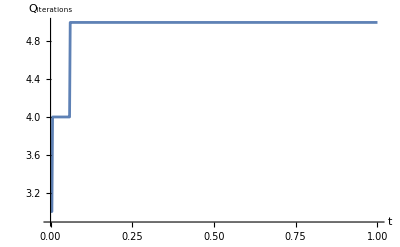

```mathematica
ListPlot[iterData,PerformanceGoal->"Speed",Joined->True, AxesLabel->{"t", "Q_iterations"}]
```

```mathematica
test1its = Import["iterationsAmount_test1_iterational", "Table",PerformanceGoal->"Speed"];
tau = 0.009;
iterData1 = Table[{i*tau,test1its[[i,1]]},{i,1,Length[test1its],1}];
```

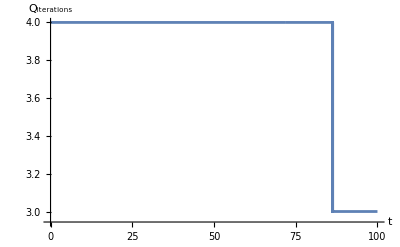

```mathematica
ListPlot[iterData1,PerformanceGoal->"Speed",Joined->True, AxesLabel->{"t", "Q_iterations"}]
```